```mathematica
proteincurvesim60s=metabgensteadystate1[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{728.903,Null}

```mathematica
proteincurve2sim60s=metabmaintainsteadystate[proteincurvesim60s[[1]],0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{744.566,Null}

```mathematica
testset=RandomInteger[400,50]
```

{353,203,6,345,293,308,94,28,159,4,357,162,123,18,5,246,164,197,5,267,203,131,114,365,313,317,136,118,262,242,296,34,71,260,366,247,212,233,124,38,11,340,250,80,267,316,291,40,137,302}

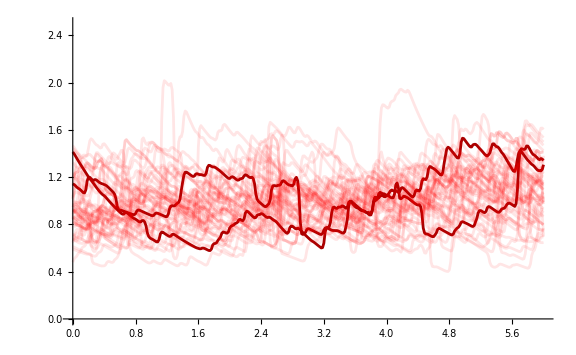

```mathematica
Show[{ListLinePlot[{Transpose@{proteincurve2sim60s[[All,1]],GaussianFilter[proteincurve2sim60s[[All,5,88]]/Mean[proteincurve2sim60s[[All,5,88]]],2]},Transpose@{proteincurve2sim60s[[All,1]],GaussianFilter[proteincurve2sim60s[[All,5,281]]/Mean[proteincurve2sim60s[[All,5,281]]],2]}},PlotRange->{{0,6},{0,2.5}},PlotStyle->Darker[Red],ImageSize->Large,AxesStyle->Directive[Black,20]],ListLinePlot[Map[Transpose@{proteincurve2sim60s[[All,1]],GaussianFilter[proteincurve2sim60s[[All,5,#]]/Mean[proteincurve2sim60s[[All,5,#]]],2]}&,testset],ImageSize->Large,PlotRange->{{0,6},{0,2.5}},PlotStyle->Directive[Opacity[0.1],Red]]}]
```

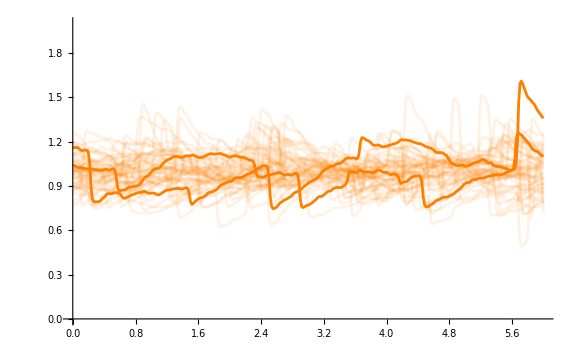

```mathematica
Show[{ListLinePlot[{Transpose@{proteincurve2sim60s[[All,1]],GaussianFilter[proteincurve2sim60s[[All,7,88]]/Mean[proteincurve2sim60s[[All,7,88]]],2]},Transpose@{proteincurve2sim60s[[All,1]],GaussianFilter[proteincurve2sim60s[[All,7,68]]/Mean[proteincurve2sim60s[[All,7,68]]],2]}},PlotRange->{{0,6},{0,2}},PlotStyle->Orange,ImageSize->Large,AxesStyle->Directive[Black,20]],ListLinePlot[Map[Transpose@{proteincurve2sim60s[[All,1]],GaussianFilter[proteincurve2sim60s[[All,7,#]]/Mean[proteincurve2sim60s[[All,7,#]]],2]}&,testset],ImageSize->Large,PlotRange->{{0,6},{0,2}},PlotStyle->Directive[Opacity[0.1],Orange]]}]
```

```mathematica
exp227rawdata=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{1.17772,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{19.967,Null}

```mathematica
comblintestexp227=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{53.1509,Null}

```mathematica
ol5000cell6h=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\ol5000cell6h.mx"];
```

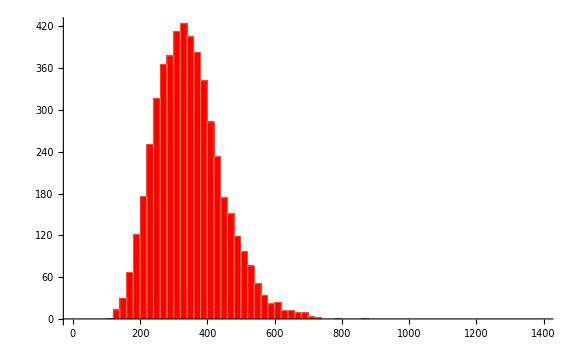

```mathematica
Histogram[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]],50,PlotRange->{{0,1400},Automatic},ChartStyle->{Red},AxesStyle->Directive[Black, 20],ImageSize->Large]
```

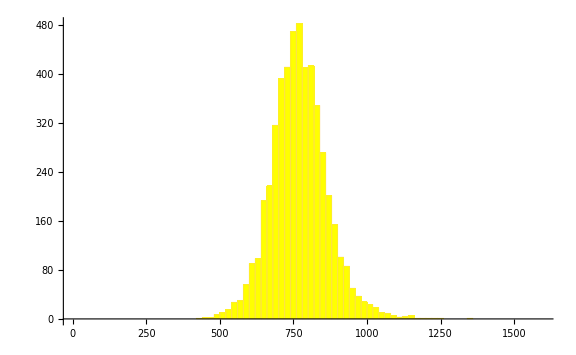

```mathematica
Histogram[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]],50,PlotRange->{{0,1600},Automatic},ChartStyle->{Yellow},AxesStyle->Directive[Black, 20],ImageSize->Large]
```

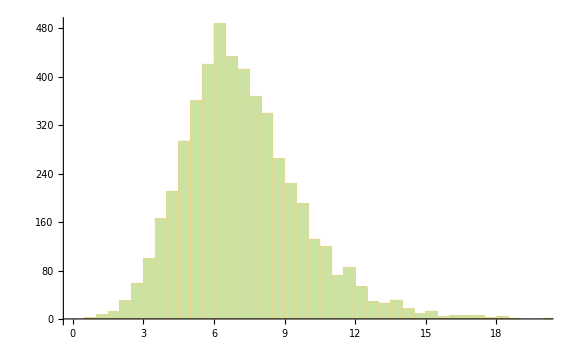

```mathematica
Histogram[ol5000cell6h[[1]][[2]]/ol5000cell6h[[1]][[6]],50,PlotRange->{{0,20},Automatic},ChartStyle->{RGBColor["#CCE2A2"]},AxesStyle->Directive[Black, 20],ImageSize->Large]
```

```mathematica
HistogramList[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]],50]
```

{{100,120,140,160,180,200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,620,640,660,680,700,720,740,760,780,800,820,840,860,880},{1,13,30,67,121,176,251,317,366,378,413,424,405,383,342,283,233,174,151,119,97,76,51,34,22,24,12,12,9,9,3,2,0,0,1,0,0,0,1}}

```mathematica
HistogramList[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]],50]
```

{{420,440,460,480,500,520,540,560,580,600,620,640,660,680,700,720,740,760,780,800,820,840,860,880,900,920,940,960,980,1000,1020,1040,1060,1080,1100,1120,1140,1160,1180,1200,1220,1240,1260,1280,1300,1320,1340,1360},{1,2,2,7,10,15,27,30,56,90,98,193,217,316,392,411,469,482,410,413,348,271,201,154,101,86,50,37,28,23,18,10,9,5,3,4,5,1,1,1,1,1,0,0,0,0,1}}

```mathematica
N[HistogramList[ol5000cell6h[[1]][[2]]/ol5000cell6h[[1]][[6]],50]]
```

{{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.},{2.,7.,12.,30.,59.,100.,166.,211.,294.,361.,421.,488.,433.,413.,368.,340.,265.,224.,190.,132.,120.,72.,85.,53.,28.,26.,31.,17.,9.,13.,4.,5.,5.,6.,2.,4.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,2.}}

```mathematica
N{{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10,21/2,11,23/2,12,25/2,13,27/2,14,29/2,15,31/2,16,33/2,17,35/2,18,37/2,19,39/2,20,41/2,21,43/2,22,45/2,23,47/2,24},{2,7,12,30,59,100,166,211,294,361,421,488,433,413,368,340,265,224,190,132,120,72,85,53,28,26,31,17,9,13,4,5,5,6,2,4,1,0,0,1,0,0,0,0,0,0,2}}
```

{{N/2,N,(3 N)/2,2 N,(5 N)/2,3 N,(7 N)/2,4 N,(9 N)/2,5 N,(11 N)/2,6 N,(13 N)/2,7 N,(15 N)/2,8 N,(17 N)/2,9 N,(19 N)/2,10 N,(21 N)/2,11 N,(23 N)/2,12 N,(25 N)/2,13 N,(27 N)/2,14 N,(29 N)/2,15 N,(31 N)/2,16 N,(33 N)/2,17 N,(35 N)/2,18 N,(37 N)/2,19 N,(39 N)/2,20 N,(41 N)/2,21 N,(43 N)/2,22 N,(45 N)/2,23 N,(47 N)/2,24 N},{2 N,7 N,12 N,30 N,59 N,100 N,166 N,211 N,294 N,361 N,421 N,488 N,433 N,413 N,368 N,340 N,265 N,224 N,190 N,132 N,120 N,72 N,85 N,53 N,28 N,26 N,31 N,17 N,9 N,13 N,4 N,5 N,5 N,6 N,2 N,4 N,N,0,0,N,0,0,0,0,0,0,2 N}}

```mathematica
Overlay[{Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,PlotRange->{{0,2.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.36,0.36,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],20],Directive[Black,20]},ImageSize->Large],Show[{Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},50,"PDF",PlotRange->{{0,2.5},Automatic},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large]}]}]
```

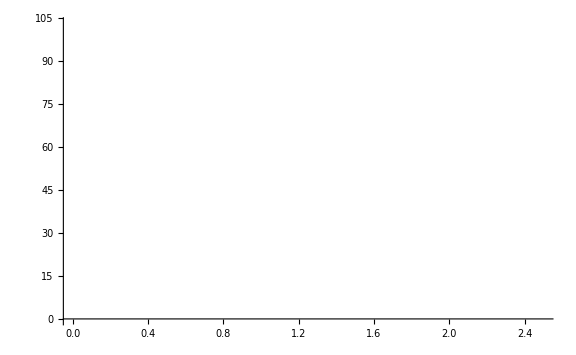
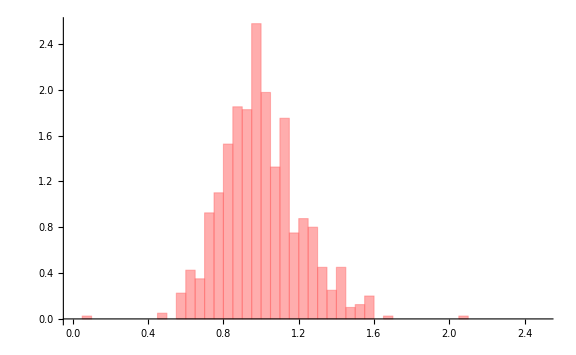
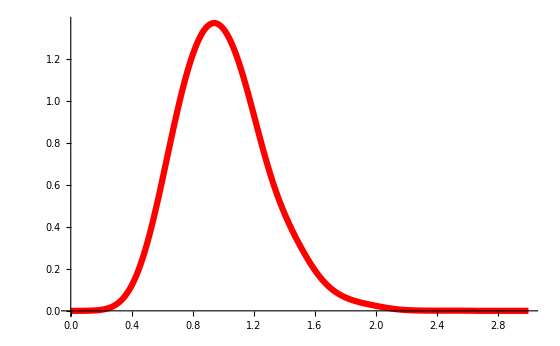

```mathematica
Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},50,"PDF",PlotRange->{{0,2.5},Automatic},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large]
```

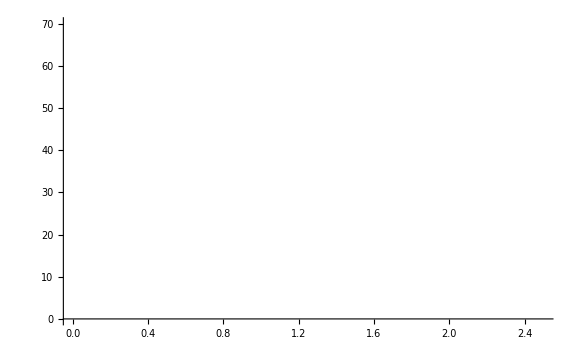
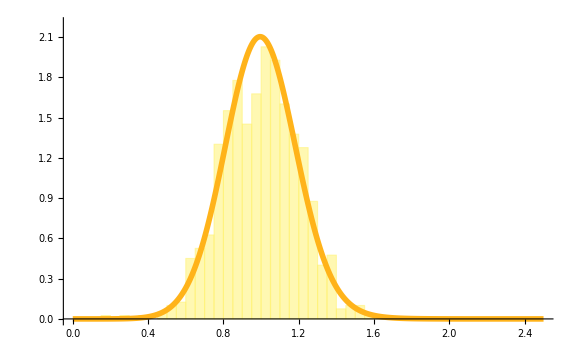

```mathematica
Overlay[{Histogram[{Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,PlotRange->{{0,2.5},{0,70}},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.95,0.4,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],20],Directive[Black,20]},ImageSize->Large],Show[{Histogram[{Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,"PDF",PlotRange->{{0,2.5},{0,2.2}},ChartStyle->RGBColor[1,0.95,0.4],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large],SmoothHistogram[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]]/Mean[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]]],.15,PlotStyle->{Thickness[0.007],RGBColor[1,0.7,0.1]},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```

```mathematica
(*Normal simulation as baseline*)
```

```mathematica
testnormal=metabgensteadystate[6,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{118.96,Null}

```mathematica
testnormalkeep=keepallmetabmaintainsteadystate[6,testnormal[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{607.366,Null}

```mathematica
testnormalmem=metabproteinmemfast[testnormalkeep];
```

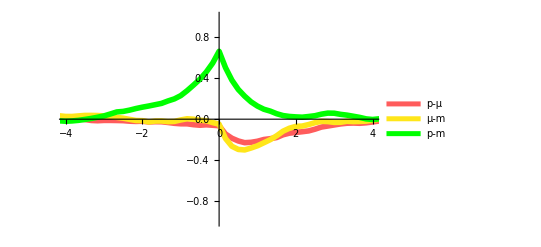

```mathematica
ListLinePlot[{testnormalmem[[4]],testnormalmem[[5]],testnormalmem[[6]]},PlotRange->{{-4,4},{-1,1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.36,0.36]],Directive[Thickness[0.01],RGBColor[1,0.9,0.1]],Directive[Thickness[0.01],Green]},AxesStyle->Directive[Black,20],PlotLegends->{"μ-p","μ-m","p-m"}]
```

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\testnormal.mx",{testnormalkeep}];
```

```mathematica
{testnormalkeep}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\testnormal.mx"];
```

```mathematica
(*constant protein copy number*)
```

```mathematica
testconstpro=metabgensteadystate[6,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{314.267,Null}

```mathematica
testconstprokeep=keepallmetabmaintainsteadystate[6,testconstpro[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{839.84,Null}

```mathematica
testconstpromem=metabproteinmemfast[testconstprokeep];
```

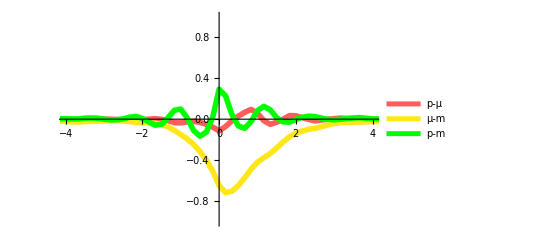

```mathematica
ListLinePlot[{testconstpromem[[4]],testconstpromem[[5]],testconstpromem[[6]]},PlotRange->{{-4,4},{-1,1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.36,0.36]],Directive[Thickness[0.01],RGBColor[1,0.9,0.1]],Directive[Thickness[0.01],Green]},AxesStyle->Directive[Black,20],PlotLegends->{"μ-p","μ-m","p-m"}]
```

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\testconstpro.mx",{testconstprokeep}];
```

```mathematica
{testconstprokeep}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\testconstpro.mx"];
```

```mathematica
(*constant growth factor*)
```

```mathematica
testconstgro=metabgensteadystate[6,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{113.53,Null}

```mathematica
testconstgrokeep=keepallmetabmaintainsteadystate[6,testconstgro[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{733.075,Null}

```mathematica
testconstgromem=metabproteinmemfast[testconstgrokeep];
```

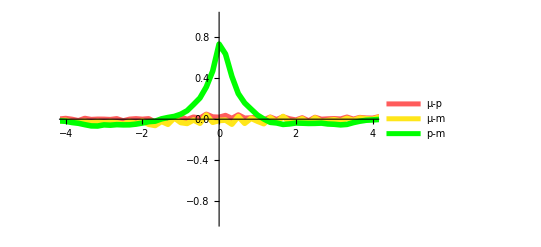

```mathematica
ListLinePlot[{testconstgromem[[4]],testconstgromem[[5]],testconstgromem[[6]]},PlotRange->{{-4,4},{-1,1}},PlotStyle->{Directive[Thickness[0.01],RGBColor[1,0.36,0.36]],Directive[Thickness[0.01],RGBColor[1,0.9,0.1]],Directive[Thickness[0.01],Green]},AxesStyle->Directive[Black,20],PlotLegends->{"μ-p","μ-m","p-m"}]
```

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\testconstgro.mx",{testconstgrokeep}];
```

```mathematica
{testconstgrokeep}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\testconstgro.mx"];
```